```mathematica
Clear["Global`*"]
g[x_] = -α x^2 +3;
h[x_] = -(Exp[x]+Exp[-x])+5;
y[x_] = Sqrt[3^2-x^2];
zero1 = x/.FindRoot[h[x],{x,-2,2}][[1]]
zero2 = x/.Solve[g[x]==0,x][[1]]
zeromax = Max[Abs[zero1],Abs[zero2]];
f[f1_,f2_]:= Sqrt[Integrate[(f1^2-f2^2)^2,{x,-zeromax,zeromax}]]
f[g[x],h[x]];
D[%,α];
(*FindRoot[%[[1]]==0,{α,1.1}]*)
```

1.5668

-(√3)/(√α)

√(3.78892-45.467 α+149.706 α^2-79.8273 α^3+12.7177 α^4)

(-45.467+299.411 α-239.482 α^2+50.8709 α^3)/(2 √(3.78892-45.467 α+149.706 α^2-79.8273 α^3+12.7177 α^4))

{{α→0.175598},{α→2.05398},{α→2.47806}}

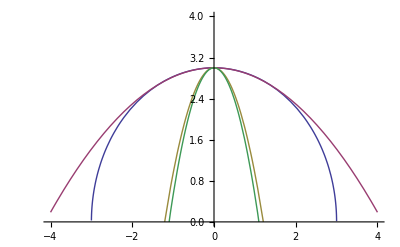

```mathematica
f[g[x],y[x]]
D[%,α]
Solve[%==0,α]
Plot[{y[x],-.175803x^2+3,-2.05398x^2 +3, -2.47806x^2+3},{x,-4,4},PlotRange->{0,4}]
```

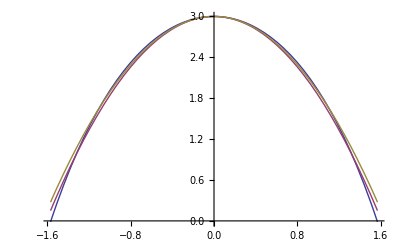

```mathematica
Plot[{-(Exp[x]+Exp[-x])+5,-1.15598x^2+3,-1.10531x^2+3},{x,-1.57,1.57}]
```

```mathematica
NSolve[-(Exp[x]+Exp[-x])+5==0,x]
```

{{x→ConditionalExpression[1. (-1.5668+(0.+6.28319 ⅈ) C[1]),C[1]∈Integers]},{x→ConditionalExpression[1. (1.5668+(0.+6.28319 ⅈ) C[1]),C[1]∈Integers]}}

```mathematica
-(Exp[-1.5668]+Exp[1.5668])
```

-5.

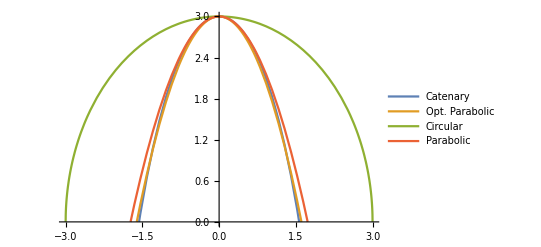

```mathematica
(*Arches*)
y1[x_] = -(Exp[x]+Exp[-x])+5;
y2[x_] = -1.15598x^2 +3;
y3[x_] =  Sqrt[3^2-x^2];
y4[x_] = -x^2 +3;
plot=Plot[{y1[x],y2[x],y3[x],y4[x]},{x,-3,3},PlotRange->{0,3},PlotLegends->{"Catenary", "Opt. Parabolic", "Circular", "Parabolic"}]
```

```mathematica
Export["arches.png",plot,ImageResolution->250]
```

arches.png

2

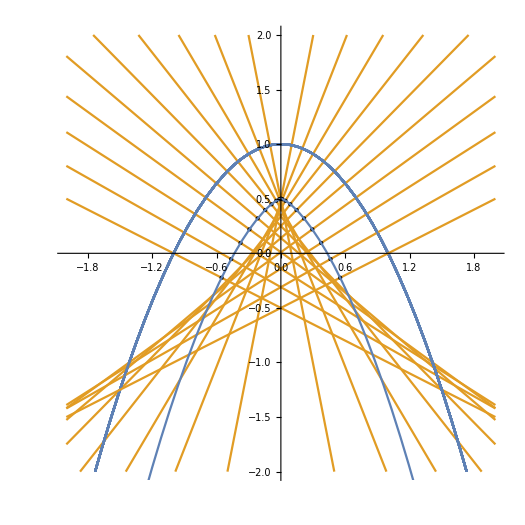

```mathematica
Clear["Global`*"]
d = 2
c = .2;
f1[x_] = -x^2 + 1;
dist = -1/2;
(*f2[x_,a_] = -2a x + f1[a] + 2 a^2;*)
f3[x_,a_] = 1/(2a) x + f1[a] - 1/2;
p1[a_] = a + 2a dist/(Sqrt[1+4a^2]);
p2[a_] = f1[a] + dist/Sqrt[1+4a^2];
plot1[c_] := Plot[{f1[x],f3[x,c]},{x,-d,d},PlotRange->{-2,2},AspectRatio->1];
t1 = Table[plot1[c],{c,-1,-.1,.1}];
t2 = Table[plot1[c],{c,.1,1,.1}];
t3 = Table[Graphics[Point[{p1[c],p2[c]}]],{c,-1,-.1,.1}];
t4 = Table[Graphics[Point[{p1[c],p2[c]}]],{c,.1,1,.1}];
plot2 = ParametricPlot[{r+dist 2r/Sqrt[1+4r^2],f1[r]+dist 1/Sqrt[1+4r^2]},{r,-d,d}];
plot3=Show[t1,t2,t3,t4,plot2]
```

```mathematica
Export["arches2.png",plot3,ImageResolution->250]
```

arches2.png

```mathematica
(*Cuastic curve
Envelope of a family of lines
Differential Eqs*)
```

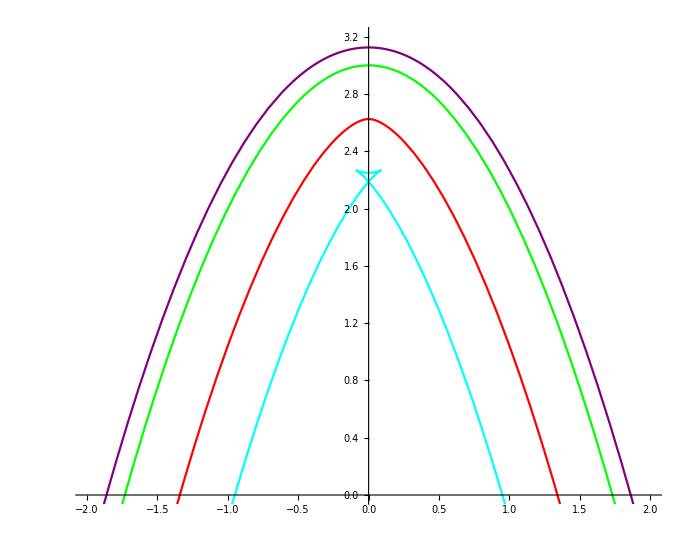

```mathematica
Clear["Global`*"]
d = 2;
a = 1;
dist1 = -1/8//N;
dist3= 3/8//N;
dist4 = 12/16//N;
p1x[x_] = x - dist1*2a x/Sqrt[1+(2a x)^2];
p1y[x_] = f2[x] - dist1/Sqrt[1+(2a x)^2];
f2[x_] = -a x^2+3;
p3x[x_] = x - dist3*2a x/Sqrt[1+(2a x)^2];
p3y[x_] = f2[x] - dist3/Sqrt[1+(2a x)^2];
p4x[x_] = x - dist4*2a x/Sqrt[1+(2a x)^2];
p4y[x_] = f2[x] - dist4/Sqrt[1+(2a x)^2];
plot1 = ParametricPlot[{p1x[r],p1y[r]},{r,-d,d},PlotStyle->Purple,PlotRange->{{-d,d},{0,3.2}}];
plot2 = Plot[f2[x],{x,-2,2},PlotStyle->Green];
plot3 = ParametricPlot[{p3x[r],p3y[r]},{r,-d,d},PlotStyle->Red];
plot4 = ParametricPlot[{p4x[r],p4y[r]},{r,-d,d},PlotStyle->Cyan];
Show[plot1,plot2,plot3,plot4]
```

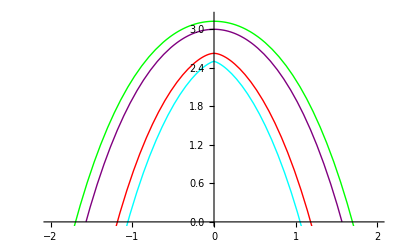

```mathematica
Clear["Global`*"];
a = 1;
b = 3+2a;
d = 2;
dist2 = 1/8;
dist3 = 3/8;
dist4 = 4/8;
f1[x_] = -a(Exp[x]+Exp[-x])+b;
p2x[x_] = x - dist2 f1'[x]/Sqrt[1+f1'[x]^2];
p2y[x_] = f1[x] + dist2/Sqrt[1+f1'[x]^2];
p3x[x_] = x + dist3 f1'[x]/Sqrt[1+f1'[x]^2];
p3y[x_] = f1[x] - dist3/Sqrt[1+f1'[x]^2];
p4x[x_] = x + dist4 f1'[x]/Sqrt[1+f1'[x]^2];
p4y[x_] = f1[x] - dist4/Sqrt[1+f1'[x]^2];
plot1 = Plot[f1[x],{x,-d,d},PlotRange->{0,3.2},PlotStyle->Purple];
plot2 =ParametricPlot[{p2x[x],p2y[x]},{x,-d,d},PlotStyle->Green];
plot3 =ParametricPlot[{p3x[x],p3y[x]},{x,-d,d},PlotStyle->Red];
plot4 =ParametricPlot[{p4x[x],p4y[x]},{x,-d,d},PlotStyle->Cyan];
Show[plot1,plot2,plot3,plot4]
```

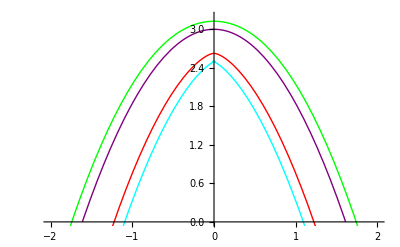

```mathematica
Clear["Global`*"];
a = 1.156;
b = 3;
d = 2;
dist2 = 1/8;
dist3 = 3/8;
dist4 = 4/8;
f1[x_] = -a x^2+b;
p2x[x_] = x - dist2 f1'[x]/Sqrt[1+f1'[x]^2];
p2y[x_] = f1[x] + dist2/Sqrt[1+f1'[x]^2];
p3x[x_] = x + dist3 f1'[x]/Sqrt[1+f1'[x]^2];
p3y[x_] = f1[x] - dist3/Sqrt[1+f1'[x]^2];
p4x[x_] = x + dist4 f1'[x]/Sqrt[1+f1'[x]^2];
p4y[x_] = f1[x] - dist4/Sqrt[1+f1'[x]^2];
plot1 = Plot[f1[x],{x,-d,d},PlotRange->{0,3.2},PlotStyle->Purple];
plot2 =ParametricPlot[{p2x[x],p2y[x]},{x,-d,d},PlotStyle->Green];
plot3 =ParametricPlot[{p3x[x],p3y[x]},{x,-d,d},PlotStyle->Red];
plot4 =ParametricPlot[{p4x[x],p4y[x]},{x,-d,d},PlotStyle->Cyan];
Show[plot1,plot2,plot3,plot4]
```

-1/(2 a)-2 a-(-a+x)/(2 a^2)

{{a→-x^(1/3)/2^(2/3)},{a→((-1)^(1/3) x^(1/3))/2^(2/3)},{a→-((-1)^(2/3) x^(1/3))/2^(2/3)}}

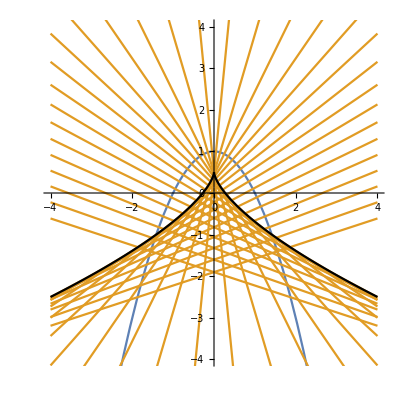

caustics.png

1/4 (2-3 2^(2/3) x^(2/3))

```mathematica
Clear["Global`*"];
d=0.5; scale = 4;
f[x_] = -x^2+1;
g[x_] = f[a]-1/f'[a] (x-a);
D[f[a]-1/f'[a] (x-a),a]
sol=Solve[D[f[a]-1/f'[a] (x-a),a]==0,a]
normalLine[x_,a_] = {x,f[a]-1/f'[a] (x-a)};
(*a = 1;*)
lines = Table[normalLine[x,a],{a,-1.55,1.55,.1}];
p1= ParametricPlot[{{-x,g[x]/.sol[[1]]},{x,g[x]/.sol[[1]]}},{x,-scale,scale},PlotRange->{{-scale,scale},{-scale,scale}},PlotStyle->{Black}];
p2= ParametricPlot[{{x,f[x]},lines},{x,-scale,scale},PlotRange->{{-scale,scale},{-scale,scale}}];
p3=Show[p2,p1]
Export["caustics.png",p3,ImageResolution->250]
g[x]/.sol[[1]]//Simplify
```

```mathematica
Integrate[Log[(1-α z^2)],z]
```

-2 z+(2 ArcTanh[z √α])/(√α)+z Log[1-z^2 α]

NDSolve::ndsz: At x == 3.48527, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[{{0., 3.48527}}, <>][x]

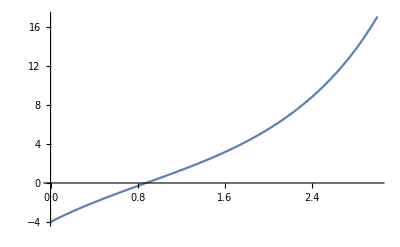

```mathematica
α = .001;
NDSolve[{z''[x]==z[x]/(1-α z[x]^2),z[0] == -4, z[1]==.5 },z[x],{x,0,5}];
p[x_] = z[x]/.%[[1]]
Plot[p[x],{x,0,3}]
```